```mathematica
ClearAll["Global`*"]
```

```mathematica
$Assumptions={θ<π/2, θ>-π/2,d>0,ϵ>0};
```

```mathematica
df[ζ_]= k  ((ζ- ⅈ)/ζ)^(θ/π);
f[ζ_]= ∫df[ζ]ⅆζ+c//FullSimplify
```

c+ⅈ k (-1-ⅈ ζ)^(θ/π) (1+ⅈ ζ)^(-θ/π) Beta[-ⅈ ζ,1-θ/π,(π+θ)/π]

```mathematica
f[0] // FullSimplify
Limit[f[I/2 + ϵ], ϵ -> 0, Direction -> -1] //Simplify
```

c

c+ⅈ ⅇ^(-ⅈ θ) k Beta[1/2,1-θ/π,(π+θ)/π]

```mathematica
c=-ⅈ d;
(*k   = (d Tan[θ]-c)/(θ+ⅈ θ Cot[θ]);*)
k =(d Tan[θ]-c)/(ⅈ ⅇ^(-ⅈ θ)  Beta[1/2,1-θ/π,(π+θ)/π]);
```

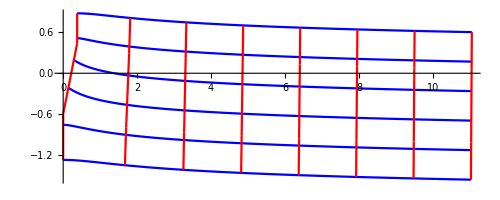

```mathematica
Block[{d=.6,θ =20*π/180,lim={.00001,10,-.5,1.5}},
Show[ParametricPlot[Array[ReIm@f[ξ+ⅈ #]&,6,lim⟦{3,4}⟧],{ξ,lim⟦1⟧,lim⟦2⟧},PlotStyle->{Blue},AspectRatio->Automatic],
 ParametricPlot[Array[ReIm@f[#+ⅈ η]&,8,lim⟦{1,2}⟧],{η,lim⟦3⟧,lim⟦4⟧},PlotStyle->{Red},AspectRatio->Automatic]]]
```

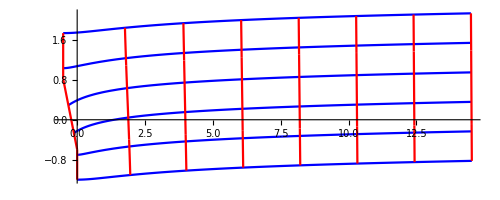

```mathematica
Block[{d=.6,θ =-20*π/180,lim={.00001,10,-.5,1.5}},
Show[ParametricPlot[Array[ReIm@f[ξ+ⅈ #]&,6,lim⟦{3,4}⟧],{ξ,lim⟦1⟧,lim⟦2⟧},PlotStyle->{Blue},AspectRatio->Automatic],
 ParametricPlot[Array[ReIm@f[#+ⅈ η]&,8,lim⟦{1,2}⟧],{η,lim⟦3⟧,lim⟦4⟧},PlotStyle->{Red},AspectRatio->Automatic]]]
```